```mathematica
;
```

Last updated:   Thu 13 Jan 2022

## About Enwonwu

```mathematica
be="Ben Enwonwu";
WolframAlpha[be,AppearanceElements->"Pods"]
```

WolframAlphaQueryResults

```mathematica
(* explore entities (and their respective properties) with the same/related name *)
findEntities[query_String]:=
```

Person | Ben Enwonwu | {AlternateNames,AstrologicalSign,BirthDate,«38»,Spouses,Weight,Wives}
SolarSystemFeature | Enwonwu crater | {AstronomicalBody,AstronomicalBodyCoordinates,«11»,StartingLongitude}

```mathematica
(* person entity *)
BE=Entity["Person","BenEnwonwu::p2thb"];
```

```mathematica
(* get more info on Ben Enwonwu *)
```

## Wikipedia

```mathematica
(* summary of Wikipedia article on Ben Enwonwu *)
textCell@WikipediaData[be,"SummaryPlaintext"]
```

Odinigwe Benedict Chukwukadibia Enwonwu MBE (14 July 1917 – 5 February 1994), better known as Ben Enwonwu, was a Nigerian painter and sculptor. Arguably the most influential African artist of the 20th century, his pioneering career opened the way for the postcolonial proliferation and increased visibility of modern African art. He was one of the first African artists to win critical acclaim, having exhibited in august exhibition spaces in Europe and the United States and listed in international directories of contemporary art. Since 1950, Enwonwu was celebrated as "Africa's Greatest Artist" by the international media and his fame was used to enlist support for Black Nationalists movement all over the world. The Enwonwu crater on the planet Mercury is named in his honour.

```mathematica
(* get full Wikipedia article and show a snippet of it *)
wikiArticle=WikipediaData[be,"ArticlePlaintext"];
```

During his time, Enwonwu was well regarded as an artist; his art is described as a "unique form of African modernism". Ogbechie describes his art as "[the opening up of] third space in art history whose nature and parameters are at variance with art history's exclusionary narratives of modernity and its inscription of the modern artist-subject as a white, Western European male”. Recognition of his bronze sculpture of the Queen proved that he, as an African modern artist, used his practice to develop a new kind of modern art whose ideals of representation and notions of artistic identity were different from conventional art-historical narrative of European modernist practice.Tutu, a series of three portraits of the Ife princess Adetutu Ademiluyi ('Tutu'), were painted by Enwonwu in 1973 and have been missing since 1975. One of the three paintings was rediscovered in 2017 in a London flat. It was sold for £1,205,000 in an auction held by Bonhams. The portrait of Tutu, one of the three made by the painter, is a Nigerian national icon and considered a reconciliation symbol between the government and Biafran separatists after the civil war.A painting by Enwonwu, titled "Owo Market" and showing a marketplace scene in the Nigerian city of Owo, and dated 1949, was restored on the BBC programme The Repair Shop, broadcast on 7 August 2019. The painting's owner had known Enwonwu, and described him as a lovely man always with a flower in his lapel and some of his work can be found in Kakofoni Group gallary


== Notable works ==
From the National Archives and Records Administration

```mathematica
(* word cloud plotting function *)
:=;
```

```mathematica
(* b-shape *)
wordCloudShape=;
```

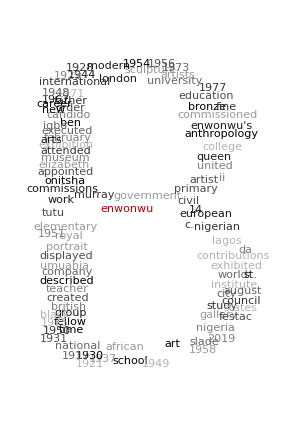
-Graphics- |  -  - art28
 -  - enwonwu22
 -  - african10
 -  - university9
 -  - london9
 -  - school8
 -  - nigeria8
 -  - murray8
 -  - lagos8
 -  - national7

```mathematica
(* plot wordcloud & show top 15 words by frequency *)
```

```mathematica
(* plots of keywords *)
Row[{g=[],},Spacer@30]
```

-Graphics--Graphics-

```mathematica
(* communities in keyword graph *)
```

-Graphics-

```mathematica
(* get from/to/see-also link rules of Wikipedia page *)
linkRules=;
linkRules=;
```

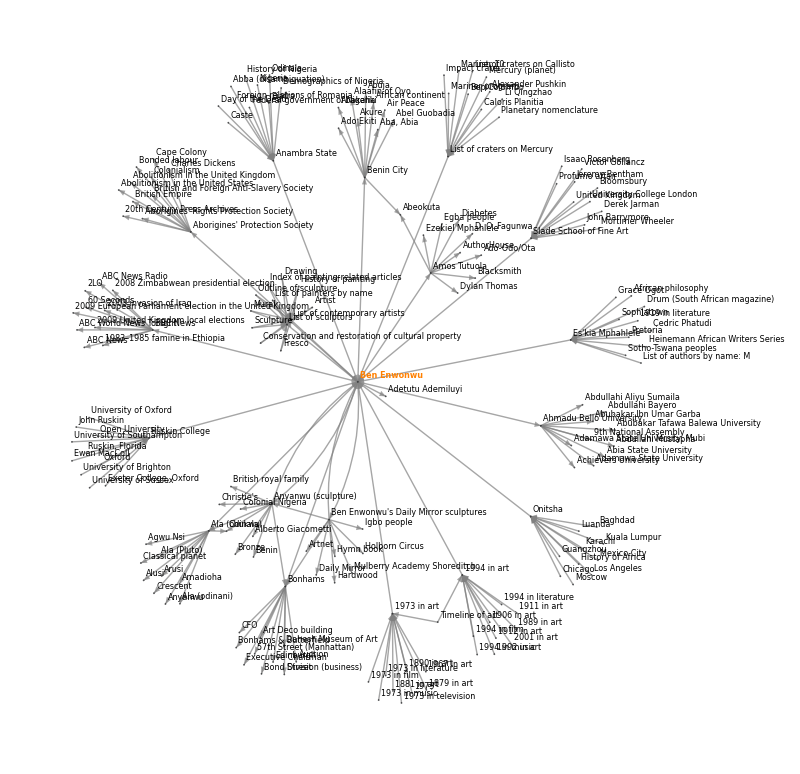

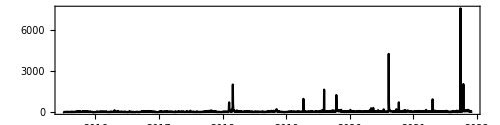

```mathematica
vLabelStyle@lbl_:=;
wg=
```

## Wikidata

```mathematica
(* BE entity on Wikidata *)
BE2=First@WikidataSearch@be
```

ExternalIdentifier[WikidataID,Q4885605,<|Label→Ben Enwonwu,Description→Nigerian Artist (1921-1994)|>]WikidataBen Enwonwuhttp://www.wikidata.org/entity/Q4885605

```mathematica
wikidataProperties=WikidataData[BE2,"Properties"];
Short[%,.1]
```

{«1»}

```mathematica
(* crater named after BE *)
BE3=First@WikidataSearch["Enwonwu"]
```

ExternalIdentifier[WikidataID,Q5381449,<|Label→Enwonwu,Description→crater on Mercury|>]WikidataEnwonwuhttp://www.wikidata.org/entity/Q5381449

```mathematica
Sort@(*[;;,;;,1,f↦f/.URL->Import]*)
```